Integrals for Line charge problem.  θ = 0,π/2,π are special cases, and have to be evaluated separately.  Also has a plot linechargeFig1.eps, and some plots (not in the book) of the integrands.

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16];
```

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

```mathematica
ClearAll[t, u, f]
$Assumptions =  t ∈ Reals ;
f[u_, t_] = (E^(I t) - u)((u^2 + 1 - 2 u Cos[t])^(-3/2));
f[u, θ]// TraditionalForm
ii = Integrate[ f[u, t], u] // FullSimplify;
ii // TraditionalForm
di = D[ii, u]// FullSimplify // TraditionalForm

iir = Integrate[ f[u, Pi/2], u] // FullSimplify;
iir// TraditionalForm
dir = D[iir, u]// FullSimplify // TraditionalForm
```

(-u+ⅇ^(ⅈ θ))/((u^2-2 u cos(θ)+1)^(3/2))

(ⅈ u csc(t)-ⅈ cot(t)+1)/(√(-2 u cos(t)+u^2+1))

(-u+ⅇ^(ⅈ t))/((-2 u cos(t)+u^2+1)^(3/2))

(1+ⅈ u)/(√(u^2+1))

-1/((u+ⅈ) √(u^2+1))

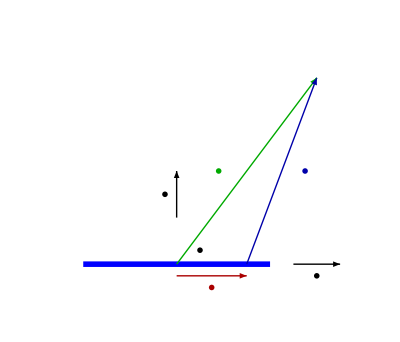

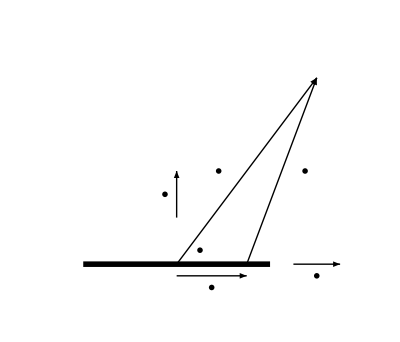

```mathematica
ClearAll[x,xp, o, e1, e2, bold, sz, fs, tsub, esub, vsub, midpoint, midtext, linechargeFig1, bwlinechargeFig1]
o = {0,0};
x = {3,4};
xp = {1.5,0};
e2 = {0,1};
e1 = {1,0};

bold = MaTeX["\\mathbf{"<>#<>"}"]&;
(*bold = Style[ #, Bold] &;
sz = 14;
fs = Style[ #, FontSize-> sz] &;*)
tsub[t_,s_] := MaTeX["\\mathbf{"<> t <>"}_{"<>ToString[s]<>"}"]
(*tsub[t_,s_] := Subscript[bold[t]// fs,s];*)
esub := tsub["e", #]&;
vsub := tsub["v", #]&;
midpoint[p_] := (p[[1]] + p[[2]])/2 ;
midtext[p_, sh_,text_] := Text[text,midpoint[p] + sh]

linechargeFig1 =Show[
ParametricPlot[{x,0}, {x,-2,2}, 
PlotStyle-> {Thickness[0.01], Blue}, (*GridLines -> Automatic,*)
Ticks->None,
Axes -> None,
PlotRange->{{-3,4}, {-1, 5}}
],
Graphics[ {
Thick,

Green// Darker,
midtext[{o,x},-0.6 e1,
MaTeX["\\color{GreenDarker}\\mathbf{x} = r \\mathbf{e}_1 e^{i \\theta}"]
],
Arrow[{o,x}],

Red//Darker,
midtext[{o,xp},-0.5 e2,
MaTeX["\\color{RedDarker}\\mathbf{x}' = x \\mathbf{e}_1"]
],
(* Arrow[{o,xp}],*)
Arrow[{o -0.25e2,xp -0.25e2} ],

Black,
Text["\\theta" // MaTeX, 0.5(e1+0.6e2)],
Arrow[{e2,2e2}],
midtext[{e2,2e2},-0.25e1,esub[3]],
Arrow[{2.5e1,3.5e1}],
midtext[{2.5e1,3.5e1},-0.25e2,esub[1]],

Blue // Darker,
Arrow[{xp,x}],
midtext[{xp,x},0.5e1, 
MaTeX["\\color{BlueDarker}\\mathbf{x} - \\mathbf{x}'"]
]
}]
]

bwlinechargeFig1 =Show[
ParametricPlot[{x,0}, {x,-2,2}, 
PlotStyle-> {Thickness[0.01], Black}, (*GridLines -> Automatic,*)
Ticks->None,
Axes -> None,
PlotRange->{{-3,4}, {-1, 5}}
],
Graphics[ {
Thick,
Black,

midtext[{o,x},-0.6 e1,
MaTeX["\\mathbf{x} = r \\mathbf{e}_1 e^{i \\theta}"]
],
Arrow[{o,x}],


midtext[{o,xp},-0.5e2,
MaTeX["\\mathbf{x}' = x \\mathbf{e}_1"]
],
 Arrow[{o -0.25e2,xp -0.25e2} ],


Text["\\theta" // MaTeX, 0.5(e1+0.6e2)],
Arrow[{e2,2e2}],
midtext[{e2,2e2},-0.25e1,esub[3]],
Arrow[{2.5e1,3.5e1}],
midtext[{2.5e1,3.5e1},-0.25e2,esub[1]],


Arrow[{xp,x}],
midtext[{xp,x},0.5e1, 
MaTeX["\\mathbf{x} - \\mathbf{x}'"]
]
}]
]
```

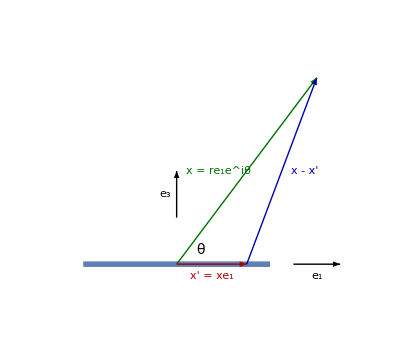

```mathematica
peeters`exportForLatex["color/linechargeFig1", linechargeFig1]
peeters`exportForLatex["bw/linechargeFig1", bwlinechargeFig1]
```

{color/linechargeFig1.eps,color/linechargeFig1pn.png}

{bw/linechargeFig1.eps,bw/linechargeFig1pn.png}

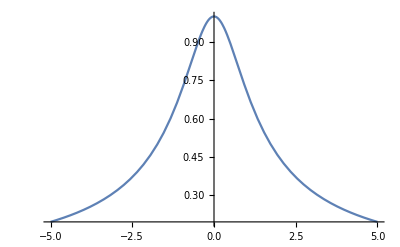

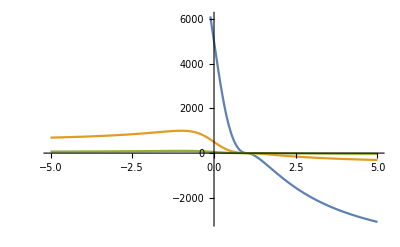

```mathematica
ClearAll[f,g, t]
f[u_] := (1 + I u)/Sqrt[1 + u^2];
g[u_, t_] := (1 - u E^(-I t)) Sqrt[1 + u^2 - 2 u Cos[t]]/(1 + u^2)/Sin[2 t];

Plot[ f[u] // Re, {u, -5, 5}]
Plot[((g[u, #] // Re) &/@ { 0.0001, 0.001, 0.01})// Evaluate,{u, -5, 5}]
```